## Useful functions

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12,Magnification->1.6};
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/31_resonances/code

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

LEC=(Λ,a_(3-1)^(S-wave) [fm],C_(2-body) [MeV],C_(3-body) [MeV])
the triton-proton S-wave scattering length is used to calibrate the core parameter and
was obtained by R. Lazauskas.

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import[NotebookDirectory[]<>"../data/a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import[NotebookDirectory[]<>"../data/LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];

activeLEC=LECsNUCLmartinrimas[[All,{1,6,7}]];
a0a1REFERENCE=a0a1NUCLmartinrimas[[All,{8,9}]];
```

(non)local resonating-group potentials from a 2- and 3-body contact interaction for TRIMER-FERMION (ABC-A)

W_(non-local) takes the Energy (e_) in [MeV]

```mathematica
NormTF[core_?ArrayQ]:=1./Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] (Pi/(core[[i]][[2]]+core[[j]][[2]]))^1.5,{i,Length[core]},{j,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_]:=Block[{eta2,eta3,w2,w3},
eta2=2. Cc/(2. (Aa+Bb)(3. Aa+3. Bb+2. lam))^(3./2.);
w2=3. (Aa+Bb) lam/(3. (Aa+Bb)+2. lam);
eta3=Dd/(6. (Aa+Bb)^2+16. (Aa+Bb) lam+2. lam^2)^(3./2.);
w3=(3. (Aa+Bb) lam ((Aa+Bb)+2. lam)/(3. (Aa+Bb)^2+8. (Aa+Bb) lam+lam^2));
eta2 Exp[-w2 r^2]+eta3  Exp[-w3 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=(27./64.)(2 (Aa+Bb))^(-3./2.) (1./TwoMyOverHBsq);
a1=(Aa+9. Bb) 3./32.;
b1=(Aa+Bb) 9./16.;
c1=(9. Aa+Bb) 3./32.;

zeta2=-27./32. Cc/(2. (Aa+Bb)+lam)^(3./2.);
zeta3=-27./64. Dd/(2  (Aa+Bb)+5 lam)^(3./2.);

a2=3. (Aa^2+9. Bb^2+10. Aa Bb+(14. Aa+18. Bb) lam)/(16. (2. (Aa+Bb)+lam));
b2=18. (Aa+Bb) ((Aa+Bb)+2. lam)/(16. (2. (Aa+Bb)+lam));
c2=3. (9. Aa^2+Bb^2+10. Aa Bb+(6. Aa+2. Bb) lam)/(16. (2. (Aa+Bb)+lam));

a3=3. (Aa^2+9. Bb^2+10. Aa Bb+(16. Aa+36. Bb) lam+27. lam^2)/(16. (2. (Aa+Bb)+5. lam));
b3=18. ((Aa+Bb)^2+4. (Aa+Bb) lam+3. lam^2)/(16. (2. (Aa+Bb)+5. lam));
c3=3. (9. Aa^2+Bb^2+10. Aa Bb+(24. Aa+4. Bb) lam+3. lam^2)/(16. (2 (Aa+Bb)+5. lam));

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2+TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

The function <SolveSecular> expects the variable <<momentum>> in  [fm^-1]
As  W_(non-local) takes the Energy (e_) in [MeV];
The core wave function is parametrized via the "a0={{c_1,α_1},{c_2,α_2},...,{c_N,α_N}}" array:
ϕ_core=(∑^N)_(i=1)c_i·e_^(-α_i/2∏_j (r^-)_j^2)

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

Amat=ConstantArray[0,{Npoints,Npoints}];

normsqu=NormTF[a00]^2;

matContainer={};

prefac=1;(*(4 π)^1.5;*)
Do[
If[a00[[ii]][[1]] a00[[jj]][[1]]≠0,

cij=a00[[ii]][[1]] a00[[jj]][[1]] normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]]],{i,1,Npoints}]];
wmat=Table[-prefac hDif^3 TwoMyOverHBsq WnolocTF[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}]; 

AppendTo[matContainer,cij (amat+wmat)];

]
,{ii,1,Length[a00]},{jj,1,Length[a00]}];

Amat=Plus[matContainer[[1]]];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat+=(Kmat+Dmat);

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);

tanDelta
]
```

numerical and physical parameters

```mathematica
nGrid=200;

nf={6,4}; (* number form for printing, only *)
k0FM=0.1;  (*initial momentum*)

rr=15.0;   (*Integration radius*)
αL=Get[LocalObject["3-1_CorePara_SwaveRimas"]]; (*what was the old αL for rimas*)

hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=Mm;
μ=m1 m2/(m1+m2);mh2=(2 μ)/(hbar)^2;
Print["E_0 = ",(k0FM hbar)^2/(2 μ)," MeV"]
λRange=Range[1,Length[activeLEC]];
```

E_0 = 0.276473 MeV

```mathematica
findLogDivisions[{xmin_,xmax_},n_Integer]:=10^FindDivisions[Log10@{xmin,xmax},n]

GetERE[x_]:=Module[{localcore=x},

core=localcore;

dataS={};dataP={};
tanDsL={};tanDpL={};
tanDs={};tanDp={};

SetSharedVariable[tanDs,tanDp];

ParallelDo[
momFM=Sqrt[2 μ energ]/hbar;
TanDelSwave=Chop[SolveSecular[rr,nGrid,momFM,0,λ,C0,D0,core,mh2]];
TanDelPwave=Chop[SolveSecular[rr,nGrid,momFM,1,λ,C0,D0,core,mh2]];
AppendTo[tanDs,{energ,TanDelSwave}];
AppendTo[tanDp,{energ,TanDelPwave}];
,{energ,ErangeMeV}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
tanDp=Reverse[Sort[tanDp,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)
(*AppendTo[tanDsL,tnDs];
AppendTo[tanDpL,tnDp];*)
(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦f1;;f2⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
Lrel = 1;
dataP=Transpose[{(Sqrt[2 μ ErangeMeV]/hbar),(Sqrt[2 μ ErangeMeV]/hbar)^3/tanDp⟦All,2⟧}];
EreP=Fit[dataP⟦f1;;f2⟧,{1,p^2},p];
a1tf=-Coefficient[EreP,p,0]^-1;
r1tf= Coefficient[EreP,p,2]*2.;
(*Print["dataS = ", dataS];*)
{a0tf,r0tf,a1tf,r1tf}
]
```

## Import density and fit wavefunctions

```mathematica
wflambdas={1,2,3,4,6,8,10};
Martinϕ1=Cases[Import["../data/abc_u_1.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ1=Transpose[{Martinϕ1⟦All,1⟧,Sqrt[Martinϕ1⟦All,3⟧]}];
Martinϕ2=Cases[Import["../data/abc_u_2.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ2=Transpose[{Martinϕ2⟦All,1⟧,Sqrt[Martinϕ2⟦All,3⟧]}];
Martinϕ3=Cases[Import["../data/abc_u_3.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ3=Transpose[{Martinϕ3⟦All,1⟧,Sqrt[Martinϕ3⟦All,3⟧]}];
Martinϕ4=Cases[Import["../data/abc_u_4.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ4=Transpose[{Martinϕ4⟦All,1⟧,Sqrt[Martinϕ4⟦All,3⟧]}];
Martinϕ6=Cases[Import["../data/abc_u_6.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ6=Transpose[{Martinϕ6⟦All,1⟧,Sqrt[Martinϕ6⟦All,3⟧]}];
Martinϕ8=Cases[Import["../data/abc_u_8.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ8=Transpose[{Martinϕ8⟦All,1⟧,Sqrt[Martinϕ8⟦All,3⟧]}];
Martinϕ10=Cases[Import["../data/abc_u_10.0_binf_r1b.dnst","Table"],{_?NumberQ,___}];
Mϕ10=Transpose[{Martinϕ10⟦All,1⟧,Sqrt[Martinϕ10⟦All,3⟧]}];
```

```mathematica
shift wave functions such that the maximum is consistently located at r=0
```

```mathematica
wfC={};
Do[
maxR=ToExpression["Mϕ"<>ToString[wflambdas[[nn]]]][[Position[ToExpression["Mϕ"<>ToString[wflambdas[[nn]]]],Max[ToExpression["Mϕ"<>ToString[wflambdas[[nn]]]][[All,2]]]][[1]][[1]]]][[1]];
AppendTo[wfC,Select[Transpose[{ToExpression["Mϕ"<>ToString[wflambdas[[nn]]]][[All,1]]-maxR,ToExpression["Mϕ"<>ToString[wflambdas[[nn]]]][[All,2]]}],#[[1]]>=0&]];
,{nn,Range[Length[wflambdas]]}
]
```

{Α1<2,Α2<2,Α3<2}

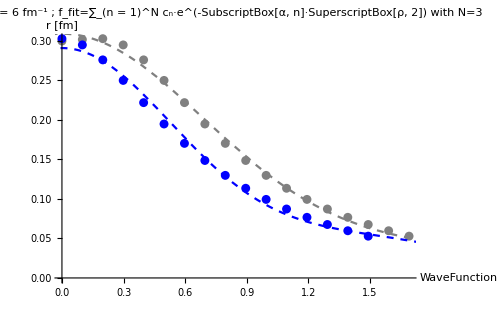

{{-20.4087,0.578139},{10.3736,0.638575},{10.3442,0.527775}}

{{-20.6703,0.897147},{10.4929,0.808381},{10.4684,1.00177}}

```mathematica
nk=3;
core={}; Do[core=AppendTo[core,ToExpression@Map[StringJoin[#,ToString[k]]&,{"C","Α"}]],{k,1,nk}];
wf=Total[Flatten[Table[core⟦i⟧⟦1⟧ⅇ^(-core⟦i⟧⟦2⟧ r^2) ,{i,Length[core]}]]];
bcs=Flatten[Table[core⟦i⟧⟦2⟧<2,{i,Length[core]}]]
(* Preliminary easy fit for starting point*)
(*core4fit8={{0.01036017979488218,0.06832713883698086},{19.485888802299826,0.2275557205094478},{-13.170079181657641,0.22755093885442249},{-6.25850055617727,0.22755176434521832},{-0.03141186053717205,10.231166883621322},{0.11494606376187202,2.046092002211391},{0.17414450554246588,0.7042170002519855},{-0.05265059942306296,0.7044119438948462}};
corefit=Transpose[{Flatten[core],Flatten[Join[core4fit8]]}];*)
wfCores={};wfCoresC={};
wfs={};wfsC={};

Do[
AppendTo[wfCores,core/.FindFit[ToExpression["Mϕ"<>ToString[wflambdas[[ll]]]],{wf,bcs},Flatten[core],r]];
corefit=Transpose[{Flatten[core],Flatten[wfCores[[-1]]]}];
AppendTo[wfs,Total[Flatten[Table[wfCores[[-1]]⟦i⟧⟦1⟧ⅇ^(-wfCores[[-1]]⟦i⟧⟦2⟧ r^2) ,{i,Length[wfCores[[-1]]]}]]]];
AppendTo[wfCoresC,core/.FindFit[wfC[[ll]],{wf,bcs},Flatten[core],r]];
corefit=Transpose[{Flatten[core],Flatten[wfCoresC[[-1]]]}];
AppendTo[wfsC,Total[Flatten[Table[wfCoresC[[-1]]⟦i⟧⟦1⟧ⅇ^(-wfCoresC[[-1]]⟦i⟧⟦2⟧ r^2) ,{i,Length[wfCoresC[[-1]]]}]]]];
,{ll,Range[Length[wflambdas]]}];

nwf=5;(*Length[wflambdas];*)
Show[ListPlot[{Select[ToExpression["Mϕ"<>ToString[wflambdas[[nwf]]]],#[[2]]>0.05&],Select[wfC[[nwf]],#[[2]]>0.05&]},PlotRange->Full,PlotStyle->{Gray,Blue}],
Plot[wfs[[nwf]],{r,-1,7},PlotStyle->{Gray,Dashed},PlotLegends->"original Ψ"],Plot[wfsC[[nwf]],{r,-1,7},PlotStyle->{Blue,Dashed},PlotLegends->"max-to-origin-shifted Ψ"],ImageSize->500, AxesLabel->{"WaveFunction","r [fm]"},
PlotLabel->"Λ = "<>ToString[wflambdas[[nwf]]]<>" fm^-1"<>"  ;  f_fit=∑_(n = 1)^N c_n·e^(-SubscriptBox[α, n]·SuperscriptBox[ρ, 2]) with N="<>ToString[nk]]
wfCores[[nwf]]
wfCoresC[[nwf]]
```

## The real pudding

```mathematica
rGrid=Subdivide[6.5,12.1,1];
rr=rGrid[[1]];
EREs={};

nGrid=200;
f1=1;f2=4; (* How many momenta should be used to make ere?*)

k0FMin=0.001;
k0FMax=0.02;
Divisions=5;

(*---------------------*)
ErangeMeV=N[findLogDivisions[{(k0FMin hbar)^2/(2 μ),(k0FMax hbar)^2/(2 μ)},Divisions]];
Erange1onfm=Sqrt[2 μ ErangeMeV]/hbar;
nwf=Length[wflambdas]-1;
Do[
Do[
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCores[[nwf]];

ERE=GetERE[mycore];
AppendTo[EREs,ERE];
Print["λ = Λ^2/4 = ",NumberForm[λ,nf](*,"  ⇒ Λ = ",NumberForm[2 Sqrt[λ],nf]," ; C_0 = ",NumberForm[C0,nf]," ; D_0 = ",NumberForm[D0,nf]*)," ; R_max = ",NumberForm[rr,nf],":   a0 = ", ERE⟦1⟧,"     r0 = ", ERE⟦2⟧,"     a1 = ", ERE⟦3⟧,"     r1 = ", ERE⟦4⟧,"   ",mycore]
,{nwf,Range[Length[wflambdas]]}];
,{rr,rGrid}];
```

λ = Λ^2/4 = 0.2500 ; R_max = 6.5000:   a0 = 6.00986     r0 = 4.00437     a1 = 51.7703     r1 = -0.670709   {{-20.6082,0.213102},{10.3225,0.203266},{10.431,0.223935}}

λ = Λ^2/4 = 1.0000 ; R_max = 6.5000:   a0 = 5.71133     r0 = 3.80609     a1 = 50.7961     r1 = -0.671596   {{-20.6639,0.344429},{10.3924,0.322455},{10.4834,0.36957}}

λ = Λ^2/4 = 2.2500 ; R_max = 6.5000:   a0 = 5.26057     r0 = 3.50172     a1 = 34.5668     r1 = -0.763129   {{-20.6362,0.432495},{10.4155,0.400739},{10.4721,0.469611}}

λ = Λ^2/4 = 4.0000 ; R_max = 6.5000:   a0 = 4.8869     r0 = 3.25314     a1 = 24.7545     r1 = -0.844472   {{-20.1516,0.495098},{10.1099,0.542862},{10.319,0.455788}}

λ = Λ^2/4 = 9.0000 ; R_max = 6.5000:   a0 = 4.48191     r0 = 2.9855     a1 = 17.0717     r1 = -0.938826   {{-20.4087,0.578139},{10.3736,0.638575},{10.3442,0.527775}}

λ = Λ^2/4 = 16.0000 ; R_max = 6.5000:   a0 = 4.25228     r0 = 2.82897     a1 = 14.6193     r1 = -0.99482   {{-20.7258,0.628374},{10.5294,0.697089},{10.5239,0.571543}}

λ = Λ^2/4 = 25.0000 ; R_max = 6.5000:   a0 = 4.02109     r0 = 2.67219     a1 = 12.4162     r1 = -1.0542   {{-19.668,0.673262},{9.99193,0.752206},{10.0198,0.60888}}

λ = Λ^2/4 = 0.2500 ; R_max = 12.1000:   a0 = 8.37991     r0 = 5.57975     a1 = 141.173     r1 = -0.476369   {{-20.6082,0.213102},{10.3225,0.203266},{10.431,0.223935}}

λ = Λ^2/4 = 1.0000 ; R_max = 12.1000:   a0 = 6.2342     r0 = 4.14674     a1 = 54.1638     r1 = -0.654722   {{-20.6639,0.344429},{10.3924,0.322455},{10.4834,0.36957}}

λ = Λ^2/4 = 2.2500 ; R_max = 12.1000:   a0 = 5.4044     r0 = 3.596     a1 = 33.5516     r1 = -0.765855   {{-20.6362,0.432495},{10.4155,0.400739},{10.4721,0.469611}}

λ = Λ^2/4 = 4.0000 ; R_max = 12.1000:   a0 = 4.94082     r0 = 3.28622     a1 = 24.7816     r1 = -0.844381   {{-20.1516,0.495098},{10.1099,0.542862},{10.319,0.455788}}

λ = Λ^2/4 = 9.0000 ; R_max = 12.1000:   a0 = 4.61622     r0 = 3.30445     a1 = 17.3258     r1 = -0.939738   {{-20.4087,0.578139},{10.3736,0.638575},{10.3442,0.527775}}

λ = Λ^2/4 = 16.0000 ; R_max = 12.1000:   a0 = 4.25945     r0 = 2.83476     a1 = 14.6327     r1 = -0.994513   {{-20.7258,0.628374},{10.5294,0.697089},{10.5239,0.571543}}

λ = Λ^2/4 = 25.0000 ; R_max = 12.1000:   a0 = 4.02313     r0 = 2.67321     a1 = 12.4081     r1 = -1.05366   {{-19.668,0.673262},{9.99193,0.752206},{10.0198,0.60888}}

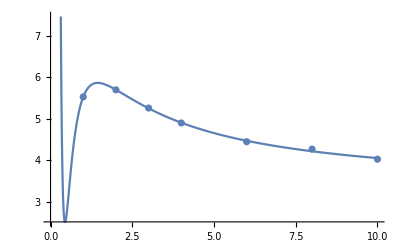

```mathematica
model=a+b/x+c/x^2+d/x^3;
data=a0s[[1]];
ft=model/.FindFit[data,model,{a,b,c,d},x];
Show[Plot[ft,{x,0,10}],ListPlot[data,PlotRange->All]]
```

```mathematica
l0=1;
a0s=Transpose[{wflambdas,er[[#]][[All,1]]}]&/@Range[Length[rGrid]];
fita0=model/.FindFit[a0s[[-1]][[l0;;]],model,{a,b,c,d},x];
r0s=Transpose[{wflambdas,er[[#]][[All,2]]}]&/@Range[Length[rGrid]];
fitr0=model/.FindFit[r0s[[-1]][[l0;;]],model,{a,b,c,d},x];
a1s=Transpose[{wflambdas,er[[#]][[All,3]]}]&/@Range[Length[rGrid]];
fita1=model/.FindFit[a1s[[-1]][[l0;;]],model,{a,b,c,d},x];
r1s=Transpose[{wflambdas,er[[#]][[All,4]]}]&/@Range[Length[rGrid]];
fitr1=model/.FindFit[r1s[[-1]][[l0;;]],model,{a,b,c,d},x];
legs="R_max="<>ToString[#]&/@rGrid;
GraphicsGrid[{{
Show[ListPlot[a0s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_S = "<>ToString[Limit[fita0,x->Infinity]]<>" fm"],Plot[fita0,{x,0,10},ImageSize->Large]],
Show[ListPlot[r0s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_S [\\textrm{fm}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_S = "<>ToString[Limit[fitr0,x->Infinity]]<>" fm"],Plot[fitr0,{x,0,10},ImageSize->Large]]
},{
Show[ListPlot[a1s,PlotLegends->Placed[legs,Above],AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["a_P [\\textrm{fm}^3]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) a_P = "<>ToString[Limit[fita1,x->Infinity]]<>" fm^3"],Plot[fita1,{x,0,10},ImageSize->Large]],
Show[ListPlot[r1s,AxesLabel->{MaTeX["\\lambda [\\textrm{fm}^{-2}]",Magnification->2],MaTeX["r_P [\\textrm{fm}^{-1}]",Magnification->2]},ImageSize->Large,PlotLabel->"lim _(λ → ∞) r_P = "<>ToString[Limit[fitr1,x->Infinity]]<>" fm^-1"],Plot[fitr1,{x,0,10},ImageSize->Large]]
}}]
```

-Graphics-

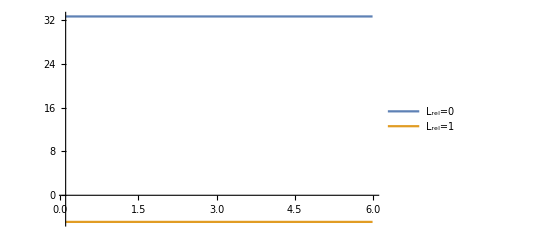

-Graphics3D-

9.

-1090.55

6552.5

```mathematica
nwf=5;
nn=Flatten[Position[activeLEC⟦All,1⟧,_?(#==wflambdas[[nwf]]&)]]⟦1⟧;
λ=0.25 activeLEC⟦nn⟧⟦1⟧^2;
C0=activeLEC⟦nn⟧⟦2⟧;D0=activeLEC⟦nn⟧⟦3⟧;
mycore=wfCoresC[[nwf]];
rprime=2.1;sca=1.;rMax=6;
Plot[{WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],0,mh2],WnolocTF[rMax,rprime,ErangeMeV[[2]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},PlotRange->Full,PlotLegends->{"L_rel=0","L_rel=1"}]

Plot3D[{(*WnolocTF[rr,rp,ErangeMeV[[-1]],λ,sca C0,sca D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2],*)WnolocTF[rr,rp,ErangeMeV[[-1]],λ,C0,D0,mycore[[1]][[2]],mycore[[2]][[2]],1,mh2]},{rr,0.1,rMax},{rp,0.1,rMax},PlotRange->Full,PlotLegends->{"E="<>ToString[ErangeMeV[[1]]],"E="<>ToString[ErangeMeV[[2]]]},PlotStyle->{Directive[Opacity[0.2],Orange, Specularity[White,50]],None},ImageSize->750]
λ
C0
D0
```